```mathematica
l1 = 0.4;
l2  = 0.25;
r2 = 0.125;
m2 = 15;
m3 = 6;
t1 = 1.6;
t2 = 0.43;
t3 = 0.01;
t4 = t2+l2^2*m3;
t5 = t1+l1^2*(m2+m3);
t6 = l1*(r2*m2+l2*m3);
t7 = t3+t4;
```

```mathematica
(*Dynamic Model of 2R manipulator*)
```

```mathematica
f1=Function[
{s1,s2,s3,s4,u1,u2},
s2
];
f2=Function[
{s1,s2,s3,s4,u1,u2},
(t7*(u1-u2+t6*(s2+s4)^2*Sin[s3])-Cos[s3]*t6*(u2-t6*s2^2*Sin[s3]))/(t7*t5-t6^2*(Cos[s3])^2)
];
f3=Function[
{s1,s2,s3,s4,u1,u2},
s4
];
f4=Function[{s1,s2,s3,s4,u1,u2},
((t5+t6*Cos[s3])*(u2-t6*s2^2*Sin[s3])-(t7+t6*Cos[s3])*(u1-u2+t6*(s2+s4)^2*Sin[s3]))/(t7*t5-t6^2*(Cos[s3])^2)
];
f5 = Function[{u1,u2},
u1^2+u2^2];
```

```mathematica
(*Runge Kutta Fourth Order*)
```

```mathematica
RungeKutta[xi1_,xi2_,xi3_,xi4_,h_,i1_,i2_]:=
(

x1 = xi1;
x2 = xi2;
x3 = xi3;
x4 = xi4;
c1 = i1;
c2=i2;

K11 =f1[x1,x2,x3,x4,c1,c2] ;
K12 = f2[x1,x2,x3,x4,c1,c2];
K13 = f3[x1,x2,x3,x4,c1,c2];
K14 = f4[x1,x2,x3,x4,c1,c2];

x1n = x1+K11*h/2;
x2n = x2+K12*h/2;
x3n = x3+K13*h/2;
x4n = x4+K14*h/2;

K21 =f1[x1n,x2n,x3n,x4n,c1,c2] ;
K22 = f2[x1n,x2n,x3n,x4n,c1,c2];
K23 = f3[x1n,x2n,x3n,x4n,c1,c2];
K24 = f4[x1n,x2n,x3n,x4n,c1,c2];

x1l = x1+K21*h/2;
x2l = x2+K22*h/2;
x3l = x3+K23*h/2;
x4l = x4+K24*h/2;

K31 =f1[x1l,x2l,x3l,x4l,c1,c2] ;
K32 = f2[x1l,x2l,x3l,x4l,c1,c2];
K33 = f3[x1l,x2l,x3l,x4l,c1,c2];
K34 = f4[x1l,x2l,x3l,x4l,c1,c2];

x1f = x1+K31*h;
x2f = x2+K32*h;
x3f = x3+K33*h;
x4f = x4+K34*h;

K41 =f1[x1f,x2f,x3f,x4f,c1,c2] ;
K42 = f2[x1f,x2f,x3f,x4f,c1,c2];
K43 = f3[x1f,x2f,x3f,x4f,c1,c2];
K44 = f4[x1f,x2f,x3f,x4f,c1,c2];

x1u = x1+(1/6)*(K11+2*K21+2*K31+K41);
x2u = x2+(1/6)*(K12+2*K22+2*K32+K42);
x3u = x3+(1/6)*(K13+2*K23+2*K33+K43);
x4u = x4+(1/6)*(K14+2*K24+2*K34+K44);

)
RungeKutta2nd[xi1_,xi2_,xi3_,xi4_,h_,i1_,i2_]:=
(
x1 = xi1;
x2 = xi2;
x3 = xi3;
x4 = xi4;
c1 = i1;
c2=i2;

K11 =f1[x1,x2,x3,x4,c1,c2] ;
K12 = f2[x1,x2,x3,x4,c1,c2];
K13 = f3[x1,x2,x3,x4,c1,c2];
K14 = f4[x1,x2,x3,x4,c1,c2];

x1n = x1+K11*h;
x2n = x2+K12*h;
x3n = x3+K13*h;
x4n = x4+K14*h;

K21 =f1[x1n,x2n,x3n,x4n,c1,c2] ;
K22 = f2[x1n,x2n,x3n,x4n,c1,c2];
K23 = f3[x1n,x2n,x3n,x4n,c1,c2];
K24 = f4[x1n,x2n,x3n,x4n,c1,c2];

x1uu = x1+(1/2)*(K11+K21);
x2uu = x2+(1/2)*(K12+K22);
x3uu = x3+(1/2)*(K13+K23);
x4uu = x4+(1/2)*(K14+K24);


)
EulerForward[xi1_,xi2_,xi3_,xi4_,h_,i1_,i2_]:=
(

x1 = xi1;
x2 = xi2;
x3 = xi3;
x4 = xi4;
c1 = i1;
c2=i2;

K11 =f1[x1,x2,x3,x4,c1,c2] ;
K12 = f2[x1,x2,x3,x4,c1,c2];
K13 = f3[x1,x2,x3,x4,c1,c2];
K14 = f4[x1,x2,x3,x4,c1,c2];

x1uu = x1+K11*h;
x2uu = x2+K12*h;
x3uu = x3+K13*h;
x4uu= x4+K14*h;

)
```

```mathematica
(*Trajectory planner*)
TrajPlan[xi1_,xi2_,xi3_,xi4_,xf1_,xf2_,xf3_,xf4_,n1_]:=
(
list = {};
n= n1;
i=1;
s10 = xi1;
s20 = xi2;
s30 = xi3;
s40 = xi4;
s1f = xf1;
s2f = xf2;
s3f = xf3;
s4f = xf4;
AppendTo[list,{s10,s20,s30,s40}];
While[
i≤ n,
s1 = s10 +(i*(1/n))*(s1f-s10);
s2 = s20 +(i*(1/n))*(s2f-s10);
s3 = s30 +(i*(1/n))*(s3f-s10);
s4 = s40 +(i*(1/n))*(s4f-s10);
AppendTo[list,{s1,s2,s3,s4}];
i++;
]
)
```

```mathematica
ModelPredictiveController[Hp_,Hc_,m1_,m2_,m3_,m4_]:=
(
InputArray1 = Array[ul1,Hc];
InputArray2 = Array[ul2,Hc];
i=1;
While[
i≤ Hp-Hc,
AppendTo[InputArray1,InputArray1[[Hc]]];
AppendTo[InputArray2,InputArray2[[Hc]]];
i++;
];
i1 =1;
st1 = m1;
st2 = m2;
st3 = m3;
st4 = m4;
objective = 0;
While[i1≤ Hp,
EulerForward[st1,st2,st3,st4,0.01,InputArray1[[i1]],InputArray2[[i1]]];
objective = objective +({100*x1uu,x2uu,100*x3uu,x4uu}-{100*π/5,0,100*π/5,0}).({100*x1uu,x2uu,100x3uu,x4uu}-{100*π/5,0,100*π/5,0});
st1 = x1uu;
st2 = x2uu;
st3 = x3uu;
st4 = x4uu;
i1++;
]

)
```

```mathematica
j=1;
ci1 = 0;
ci2 = 0;
ci3 = 0;
ci4 = 0;
```

```mathematica
list1 = {};
list2={};
list3 = {};
list4 = {};
AppendTo[list1,0];
AppendTo[list2,0];
AppendTo[list3,0];
AppendTo[list4,0];

While[j<100,
ModelPredictiveController[3,2,ci1,ci2,ci3,ci4];
b=Join[InputArray1,InputArray2];
t=NMinimize[{objective,Abs[b]≤ 10},b];
u1 = ul1[1]/.t[[2]][[1]];
u2 = ul2[1]/.t[[2]][[3]];
EulerForward[ci1,ci2,ci3,ci4,0.01,u1,u2];
ci1 = x1uu+RandomReal[0.001];
ci2 = x2uu;
ci3 = x3uu+RandomReal[0.001];
ci4 = x4uu;

AppendTo[list1,ci1];
AppendTo[list2,ci2];
AppendTo[list3,ci3];
AppendTo[list4,ci4];
j++;
]
```

# Energy optimal control

```mathematica
(*ForwardEularforEnergy[xi1_,xi2_,xi3_,xi4_,xi5_,h_,i1_,i2_]:=
(
x1 = xi1;
x2 = xi2;
x3 = xi3;
x4 = xi4;
x5 = xi5;
c1 = i1;
c2=i2;

K11 =f1[x1,x2,x3,x4,c1,c2] ;
K12 = f2[x1,x2,x3,x4,c1,c2];
K13 = f3[x1,x2,x3,x4,c1,c2];
K14 = f4[x1,x2,x3,x4,c1,c2];
K15 = f5[c1,c2];

x1uu = x1+K11*h;
x2uu = x2+K12*h;
x3uu = x3+K13*h;
x4uu= x4+K14*h;
x5uu = x5+K15*h;
)
Ndisc = 40;
i=1;
xi1 = 0;
xi2 = 0;
xi3 = 0;
xi4 = 0;
xi5 = 0;
InputArray1 = Array[ul1,Ndisc-1];
InputArray2 = Array[ul2,Ndisc-1];
StateArray1 = Array[s1,Ndisc];
StateArray2 = Array[s2,Ndisc];
StateArray3 = Array[s3,Ndisc];
StateArray4 = Array[s4,Ndisc];
StateArray5 = Array[s5,Ndisc];
i=2;
u1 = InputArray1 [[1]];
u2 = InputArray2 [[1]];


obj1 =(StateArray1[[1]]-0)^2;
obj2 =(StateArray2[[1]]-0)^2;
obj3 =(StateArray3[[1]]-0)^2;
obj4 =(StateArray4[[1]]-0)^2;
obj5 =(StateArray5[[1]]-0)^2;


While[i≤ Ndisc,
x1 = StateArray1[[i-1]];
x2= StateArray2[[i-1]];
x3 = StateArray3[[i-1]];
x4 = StateArray4[[i-1]];
x5 = StateArray5[[i-1]];
u1 = InputArray1 [[i-1]];
u2 = InputArray2 [[i-1]];
ForwardEularforEnergy[x1,x2,x3,x4,x5,0.01,u1,u2];
obj1 = obj1+(StateArray1[[i]]-x1uu)^2;
obj2 = obj2+(StateArray2[[i]]-x2uu)^2;
obj3 = obj3+(StateArray3[[i]]-x3uu)^2;
obj4 =obj4+ (StateArray4[[i]]-x4uu)^2;
obj5= obj5+(StateArray5[[i]]-x5uu)^2;
i++;
]

obj1=obj1+10^8*( π/5-StateArray1[[Ndisc]])^2;
obj2 =obj2+10^8*( 0-StateArray2[[Ndisc]])^2;
obj3 =obj3+10^8*( π/5-StateArray3[[Ndisc]])^2;
obj4 =obj4+10^8*( 0-StateArray4[[Ndisc]])^2;
b = Join[StateArray1,StateArray2,StateArray3,StateArray4,StateArray5, InputArray1, InputArray2 ]
obj = 1000*StateArray5[[Ndisc]]+10^8*(obj1+obj2+obj3+obj4+obj5);*)
```

```mathematica
(*obj;
r = NMinimize[obj,b]
```

```mathematica
(*s1m = StateArray1/.r[[2]]
s2m = StateArray2/.r[[2]]
s3m = StateArray3/.r[[2]]
s4m = StateArray4/.r[[2]]
s5m = StateArray5/.r[[2]]
u1m = InputArray1/.r[[2]]
u2m = InputArray2/.r[[2]]*)
```

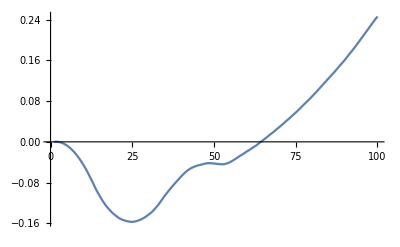

```mathematica
ListLinePlot[list1]
```

```mathematica
ListPlot[0.604805919145]
```

ListPlot::lpn: 0.604806 is not a list of numbers or pairs of numbers.

ListPlot[0.604806]